```mathematica
ClearAll["Global`*"]
```

#### Parameters;

```mathematica
imgSz=300;
```

#### R - operators;

```mathematica
V[x_,y_]:=x+y+Sqrt[x^2+y^2]
Λ[x_,y_]:=-V[-x,-y]
band[a_,x_]:=1/(2a)(a^2-x^2)
line[a_,b_,c_,x_,y_]:=(a x + b y + c)/Sqrt[a^2+b^2]
```

#### Geometry (dimensionless);

```mathematica
L=1;
H=L/2;
Tc=0;
Th=1;
```

#### Coircone CC;

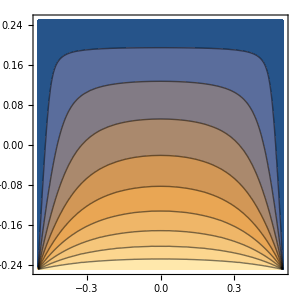
-Graphics3D--Graphics-

```mathematica
ωC[x_,y_]:=Λ[band[H,x],H/2-y];
ωH[x_,y_]:=y+H/2;
ω[x_,y_]:=Λ[ωC[x,y],ωH[x,y]];
F[x_,y_]:=(ωC[x,y]Th+ωH[x,y]Tc)/(ωC[x,y]+ωH[x,y]);

Row@{Plot3D[F[x,y],{x,- L/2,L/2},{y,- H/2,H/2},PlotRange->Full,Mesh->None,ImageSize->imgSz],
ContourPlot[F[x,y],{x,- L/2,L/2},{y,- H/2,H/2},PlotRange->Full,Mesh->None,ImageSize->imgSz]}
```

#### Coircone HC;

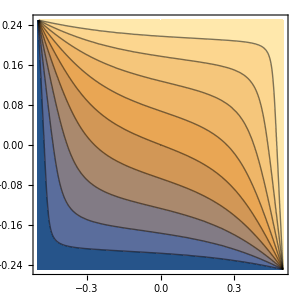
-Graphics3D--Graphics-

```mathematica
ωC[x_,y_]:=Λ[x+L/2,y+H/2];
ωH[x_,y_]:=Λ[L/2-x,H/2-y];
ω[x_,y_]:=Λ[ωC[x,y],ωH[x,y]];
F[x_,y_]:=(ωC[x,y]Th+ωH[x,y]Tc)/(ωC[x,y]+ωH[x,y]);

Row@{Plot3D[F[x,y],{x,- L/2,L/2},{y,- H/2,H/2},PlotRange->Full,Mesh->None,ImageSize->imgSz],
ContourPlot[F[x,y],{x,- L/2,L/2},{y,- H/2,H/2},PlotRange->Full,Mesh->None,ImageSize->imgSz]}
```

#### Coircone HH;

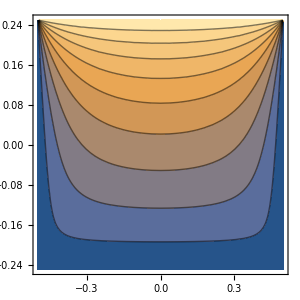
-Graphics3D--Graphics-

```mathematica
ωC[x_,y_]:=Λ[band[L/2,x],y+H/2];
ωH[x_,y_]:=H/2-y;
ω[x_,y_]:=Λ[ωC[x,y],ωH[x,y]];
F[x_,y_]:=(ωC[x,y]Th+ωH[x,y]Tc)/(ωC[x,y]+ωH[x,y]);

Row@{Plot3D[F[x,y],{x,- L/2,L/2},{y,- H/2,H/2},PlotRange->Full,Mesh->None,ImageSize->imgSz],
ContourPlot[F[x,y],{x,- L/2,L/2},{y,- H/2,H/2},PlotRange->Full,Mesh->None,ImageSize->imgSz]}
```

#### Rote;

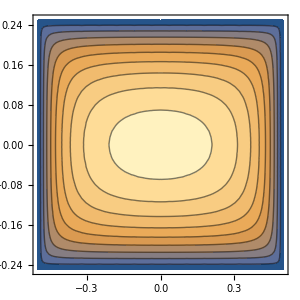
-Graphics3D--Graphics-

```mathematica
ωC[x_,y_]:=L/2-x;
ωH[x_,y_]:=L/2+x;
ω1[x_,y_]:=band[L/2,x];
ω2[x_,y_]:=band[H/2,y];
ω[x_,y_]:=Λ[ω1[x,y],ω2[x,y]]
(*ω[x_,y_]:=Λ[ωC[x,y],ωH[x,y]];*)
F[x_,y_]:=(ωC[x,y]Th+ωH[x,y]Tc)/(ωC[x,y]+ωH[x,y]);

Row@{Plot3D[ω[x,y],{x,- L/2,L/2},{y,- H/2,H/2},PlotRange->Full,Mesh->None,ImageSize->imgSz],
ContourPlot[ω[x,y],{x,- L/2,L/2},{y,- H/2,H/2},PlotRange->Full,Mesh->None,ImageSize->imgSz]}
```